```mathematica
Clear["Global`*"]
```

# Analytical Solution

## Cory Aitchison - January 2022

Working out to find the coefficients of u^(1) such that L[u^(1) + u^(0)] + N[u^(0)] = 0, up to third order terms.

## Set Up

### Miscellaneous

```mathematica
CC[x_]:=Cos[σ x] / Cosh[σ x];
SS[x_]:=Sin[σ x] / Sinh[σ x];
LDE[f_]:=D[f[x],{x,4}] + 4 σ^4 f[x] ;
NDE[f_]:=Γ f[x]^3;
```

### Ansatz

```mathematica
u[n_]:=x|->Sum[c[i]CC[x]^((2n+1)-i) SS[x]^(i), {i, 0, 2n+1}];
u[0] := x |->A CC[x] + B SS[x];
```

### Numerical Values

```mathematica
param = {σ-> 6^(1/4), Γ -> -24};
estimates = {A -> 0.4384, B -> 1.0170};
```

## Solution

### Simplifying Hyp Trig

We first convert the hyperbolic trig terms into sinh and cosh variables, so that Mathematica doesn’t automatically simplify them

```mathematica
eq1 := LDE[x |-> u[0][x] + u[1][x]] + NDE[u[0]];
```

```mathematica
notrig = {
Cosh[_] -> cosh, Sinh[_]->sinh,
Tanh[_] -> sinh / cosh, Coth[_] -> cosh / sinh, 
Sech[_] -> 1/cosh,  Csch[_] -> 1/sinh
};
```

```mathematica
eq2 := eq1 //. notrig // Together;
```

```mathematica
Denominator[eq2]
```

cosh^7 sinh^7

By using Together[], we write it as a fraction over a common denominator, which is 1/cosh^7sinh^7. Therefore, to look for third order terms, we want the numerator terms that are of the form cosh^11, cosh^10 sinh^1, etc.

```mathematica
eq3 := Numerator[eq2];
```

We can then use hyp trig identity cosh^2 - sinh^2 = 1 to reduce the terms further.

```mathematica
htrigident = {
cosh^k_-> (1+sinh^2)^(Floor[k/2]) cosh^(Mod[k,2])
};
```

```mathematica
eq4 := eq3 //. htrigident//Expand;
```

### Extracting Coefficients

Now that it is all simplified as far as possible, we can extract the coefficients that give us 11th powers (for the numerator). There will be two: cosh * sinh^10, and sinh^11.

```mathematica
list1 := CoefficientList[eq4, {sinh, cosh}];
```

```mathematica
list2 := {
list1[[11,2]], (* sinh^10 cosh^1 *)
list1[[12,1]]     (* sinh^11 cosh^0 *)
};
```

### Simplifying Trig

These two terms should be identically zero. To find the conditions on c[...] that make this so, we need to simplify the trig terms using cos^2 + sin^2 = 1:

```mathematica
trigident = {
Cos[x σ]^k_-> (1-Sin[x σ]^2)^(Floor[k/2]) Cos[x σ]^(Mod[k,2])
};
```

```mathematica
list3 :=CoefficientList[list2 /. trigident, {Cos[x σ], Sin[x σ]}];
```

We select only the nonzero coefficients which we need to solve for:

```mathematica
(list4 = list3 // Flatten // Select[Not@*PossibleZeroQ]) // MatrixForm
```

(3 A^2 B Γ-24 A σ^4+8 B σ^4+72 σ^4 c[0]-232 σ^4 c[1]+24 σ^4 c[2]+264 σ^4 c[3]
-3 A^2 B Γ+B^3 Γ+320 σ^4 c[1]-320 σ^4 c[3]
A^3 Γ-8 A σ^4-24 B σ^4-56 σ^4 c[0]-24 σ^4 c[1]+88 σ^4 c[2]-72 σ^4 c[3]
-A^3 Γ+3 A B^2 Γ+320 σ^4 c[0]-320 σ^4 c[2])

### Solution

```mathematica
answer = Solve[list4 == 0, {c[0], c[1], c[2], c[3]}][[1]] // Simplify // Apart
```

{c[0]→A/4+(-2 A^3 Γ-9 A^2 B Γ-6 A B^2 Γ-9 B^3 Γ)/(1280 σ^4),c[1]→-B/4+(3 (3 A^3 Γ+2 A^2 B Γ+3 A B^2 Γ-2 B^3 Γ))/(1280 σ^4),c[2]→A/4-(3 (2 A^3 Γ+3 A^2 B Γ-2 A B^2 Γ+3 B^3 Γ))/(1280 σ^4),c[3]→-B/4+(9 A^3 Γ-6 A^2 B Γ+9 A B^2 Γ-2 B^3 Γ)/(1280 σ^4)}

```mathematica
answer /. param /. estimates
```

{c[0]→0.15371,c[1]→-0.253315,c[2]→0.137759,c[3]→-0.259133}

## Plots

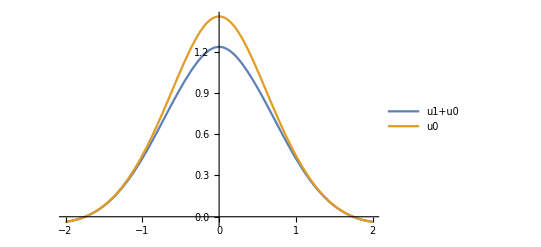

```mathematica
Plot[
{
u[0][x]+u[1][x] /. answer /. param /. estimates,
u[0][x] /. param /. estimates 
},
{x,-2,2}, 
PlotLegends->{"u1+u0", "u0"}
]
```